```mathematica
Problem 1
A cake with three regions has to be divided among two people with values: 
19 0 81
0 20 80
We can find a sum-maximizing division with this command:
```

```mathematica
FindMaximum[{(81x+19)+(80(1-x)+20),0≤x≤1},x]
```

{120.,{x→1.}}

To maximize the sum of roots we can do:

```mathematica
LinguisticAssistant
```

```mathematica
FindMaximum[{(81x+19)^0.5+(80 (1- x)+20)^0.5,0≤x≤1},x]
```

```mathematica
{15.460123935427085,{x->0.5123265074245645}}
```

48.52

To maximize the product of values - which gives an envy-free allocation - we do:

```mathematica
FindMaximum[{Log[81x+19]+Log[80(1-x)+20],0≤x≤1},x]
```

```mathematica
{8.180428936853293,{x->0.5077160478375867}}
```

```mathematica
Problem 2
```

A cake with four regions has to be divided among 3 people with values: 
19 0 0 81
0 20 0 80
0 0 40 60
We can find a product-maximizing division with this command:

```mathematica
Welfare[x_,y_,z_]:=Log[81x+19]+Log[80 y+20]+Log[60z+40]
```

```mathematica
FindMaximum[{Welfare[x,y,z],0<x<1, 0<y<1,0<z<1, x+y+z==1},{x,y,z}]
```

{11.8731,{x→0.48251,y→0.467078,z→0.0504124}}

```mathematica
Or with this command:
```

```mathematica
Welfare2[x_,y_] := Welfare[x,y,1-x-y]
```

```mathematica
FindMaximum[{Welfare2[x,y],0<x<1,0<y<1,0<x+y<1},{{x,0},{y,0}}]
```

{11.8731,{x→0.48251,y→0.467078}}

Here is the optimal solution in a plot:

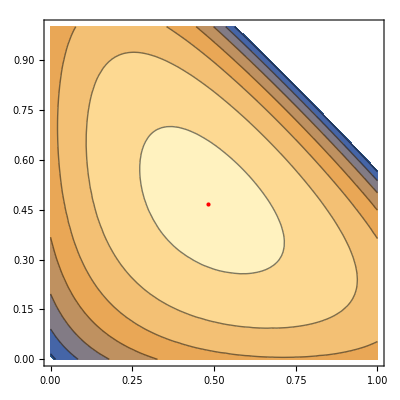

```mathematica
Show[ContourPlot[Welfare2[x,y],{x,0,1},{y,0,1}],Graphics[{Red,PointSize[Large],Point[{x,y}/.Last[%]]}]]
```

NMaximize calculates a global maximum. In this case it is identical to the local maximum of FindMaximum:

```mathematica
NMaximize[{Welfare2[x,y],0<x<1,0<y<1,0<x+y<1},{x,y}]
```

{11.8731,{x→0.48251,y→0.467078}}

```mathematica
Welfare3[x_,y_]:=(81x+19)+(80 y+20)+(60(1-x-y)+40)
```

```mathematica
NMaximize[{Welfare3[x,y],0<x<1,0<y<1,0<x+y<1},{x,y}]
```

{160.,{x→1.,y→0.}}

```mathematica
NMaximize[{Welfare3[x,y],{0≤x≤1,0≤y≤1,x+y≤1}},{x,y}, Integers]
```

{160.,{x→1,y→0}}

```mathematica
FindMaximum[{Log[3m1+2p1+d1]+Log[6m2+5p2+4d2]+Log[9(1-m1-m2)+8(1-p1-p2)+7(1-d1-d2)], 0≤m1+m2≤1,0≤d1+d2≤1,0≤p1+p2≤1,0≤m1≤1,0≤m2≤1,0≤p1≤1,0≤p2≤1,0≤d1≤1,0≤d2≤1},{{m1,0.1},{m2,0.1},{p1,0.1},{p2,0.1},{d1,0.1},{d2,0.1}}]
```

{4.67925,{m1→0.854165,m2→0.145833,p1→4.55487×10^-7,p2→0.849998,d1→2.85534×10^-7,d2→1.84868×10^-6}}